## Using the Basic NEX Reader as a Java Object

### Updated 13.11 .07

```mathematica
<<NounouM2`
```

```mathematica
InstallJava[];
```

```mathematica
LoadJavaClass["nounous.data.Range", StaticsVisible->True]
```

JavaClass[nounous.data.Range,<>]

```mathematica
tempret=JavaNew["nounous.reader.ReaderNEX"]
```

«JavaObject[nounous.reader.ReaderNEX]»

```mathematica
(*xDataObj=tempret@read["\\\\Herakles\\VSDdata\\_results\\_disp\\131105a\\2013-11-05_15-15-06\\SE-CSC-Ch1.nex"]*)
```

```mathematica
xDataObj=tempret@read["V:\\data\\disp\\2013-11-05_15-15-06\\SE-CSC-Ch1.nex"]
```

«JavaObject[scala.collection.immutable.$colon$colon]»

```mathematica
xDataObj=xDataObj@apply[0]
```

«JavaObject[nounous.data.XDataArray]»

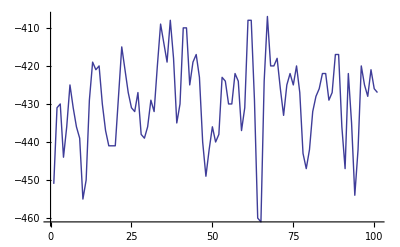

```mathematica
ListLinePlot[xDataObj@readTraceAbs[0,range[0,100]]]
```

```mathematica
Methods[xDataObj]
```

double absGain()
double absOffset()
String absUnit()
int channelCount()
String channelName(int)
String[] channelNames()
int[][] data()
boolean equals(Object)
double frameToTime(int)
Class getClass()
int hashCode()
boolean isCompatible(nounous.data.X)
int length()
void notify()
void notifyAll()
boolean rangeCheck(scala.Tuple2)
int[][] read()
int[] readFrame(int)
double readPointAbs(int, int)
int readPoint(int, int)
double[] readTraceAbs(int)
int[] readTrace(int)
int[] readTrace(int, scala.Tuple2)
double sampling()
double start()
int timeToFrame(double)
double toAbs(int)
double[] toAbs(int[])
double[][] toAbs(int[][])
String toString()
void wait(long, int) throws InterruptedException
void wait(long) throws InterruptedException
void wait() throws InterruptedException
int xBits()
double xBitsD()
nounous.data.X $colon$colon$colon(nounous.data.X)